### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/13

### Keywords

Details

# Model 1.3

Model 1.3 is the model for the dynamics of malaria parasites (P. falciparum) in a patient during treatment with artesunate proposed by Hoshen and colleagues (Hoshen, et al., (2000) Mathematical modelling of the chemotherapy of Plasmodium falciparum malaria with artesunate: postulation of 'dormancy', a partial cytostatic effect of the drug, and its implication for treatment regimens Parasitology 121 ( Pt 3), 237-246). At every time step of this model, some parasites are in the dormancy stage. In this stage it is assumed that the parasites cannot be killed by the drug and cannot be observed in the peripheral blood for a period of time.

Hoshen's model is based on White's model (White et al., (1992) The effects of multiplication and synchronicity on the vascular distribution of parasites in falciparum malaria Transactions of the Royal Society of Tropical Medicine and Hygiene 86, 590-597) that is the age distribution of parasties on admission follows a normal distribution. All parasites have the same mutiplication rate and life-span.

The model assumes that the parasties at very young age and very mature age are not sensitive to artesunate (See Figure below; it is from Fig.1 of Hoshen, et al.(2000) Parasitology). In this model 1.3, the efficacy of artesunate is calculated from the DHA concentration data that user must have as the input for the model.

-Graphics-

model | model ID
lifecycle | the parasites life-span (hours)
initn | the initial number of parasites on admissioin
mu | the mean age of parasites on admission (hours)
sigma | the standard of the age of parasites on admission (hours)
pmr | parasite multiplication rate (per life-cyle)
everyh | duration (hours) between each dose of artesunate
ndrug | the number of doses
concfile | the file name of DHA concentration data
ec50 | the DHA concentrantion at 50% efficacy
dortime | dormancy period (hours)
dorfrac | dormancy fraction
runmax | the maximum runtime of the model (hours)
outform | the output form

List of the parameters for model 1.3.

Model 1.3 has three output forms. See the table below.

0 | show the number of circulating parasites over time.
1 | write log10(number of circulating parasites) of every time step (hour) to "modgen.csv".
2 | show log10(number of circulating parasites) of every time step (hour).

Values of outform for model 1.3.

The example of the output of model 1.3.

******INDIVARIA*****

model: 1.3

outform: 2

********************

model: 1.3

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

concfile: P002.csv

everyh: 24

ndrug: 7

ec50: 38.2193

runmax: 70

dorfrac: 0.05

dortime: 7

outform: 2

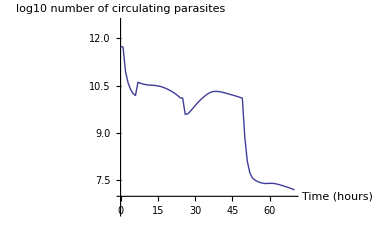

```mathematica
ListLinePlot[IDVL["mod1_3.in"],PlotRange->{6.5,12.5},FrameLabel->{"Time (hours)","Log10 Observed Parasites"},Joined->True,AxesLabel->{"Time (hours)","log10 number of circulating parasites"}]
```

More About

List of models

Related Tutorials

Using Indivaria

Related Wolfram Education Group Courses